## Star - Disk magnetic field interaction

### Setup

```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
SetDirectory["/home/dagl4841/ResearchLocal/netFieldEvo/mathematica"];
```

```mathematica
rloglog[functions_,yLabel_,legendLabels_,coords_]:=LogLogPlot[functions, {r,rMin,rMax}, Frame->True,FrameLabel->{"r (AU)", yLabel},ImageSize->Large,PlotLegends->legendLabels,BaseStyle->{FontWeight->"Bold",FontSize->14},PlotRange->Full, GridLines->coords]
```

```mathematica
au=1.5*10^13;
G=6.67*10^-8;
Msun=2*10^33;
mp=1*10^-24;
kb=1.38*10^-16;
year=3.15*10^7;
rMin=r0star;
rMax=100;
```

```mathematica
starSizeFactor = 1.0;
Mstar=starSizeFactor*Msun;
```

### Stellar field

```mathematica
B0star = 1000; (* typical polar field at the sun's surface is about 1 gauss, more like 1000 gauss for t-tauri *)
r0star=starSizeFactor^3*0.01; (* 1/200 of an AU is roughly photosphere *)
Bstar[r_]:=B0star*(r/r0star)^-3 (* dipole falloff *)
```

### MMSN model

```mathematica
(* input r is in au, other quantities are in cm *)
r0disk=1;
μ=2.7;
Σ[r_]:=1700 * (r/r0disk)^(-3/2); 
T[r_]:=280*(r/r0disk)^(-1/2)
cs[r_]:=√((kb T[r])/(μ mp)) ;
Ω[r_]:=√((G Mstar)/(r*au)^3)
h[r_]:=cs[r]/Ω[r];
hor[r_]:=h[r]/(r*au)
ρ[r_]:=1/(√(2π))Σ[r]/h[r];
P[r_]:=ρ[r]*cs[r]^2;
```

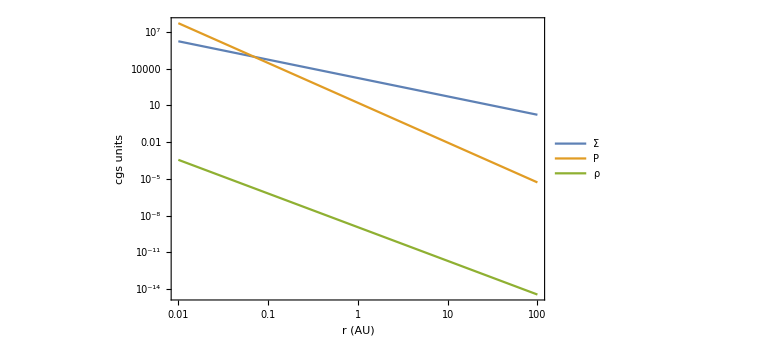

```mathematica
rloglog[{Σ[r],P[r], ρ[r]}, "cgs units",{"Σ","P","ρ"},{{},{}}]
```

```mathematica
Log10[P[10]/P[1]]
```

-3.25

### Randomly oriented disk field: assume constant β

```mathematica
βrand[r_]:= 10^5; (* complete guess *)
Brand[r_]:=√(βrand[r]^-1*P[r])
```

### Net disk field (without star influence): assume power law, define β at some point

```mathematica
(* this is harder *)
Bnet0=Brand[1];
n=0.5;
Bnet[r_]:=Bnet0*(r/5)^-n
Bnet1[r_]:=0.1*Bnet0*(r/5)^-n
Bnet2[r_]:=0.32*Bnet0*(r/5)^-n
Bnet3[r_]:=1*Bnet0*(r/5)^-n
Bnet4[r_]:=3.2*Bnet0*(r/5)^-n
Bnet5[r_]:=10*Bnet0*(r/5)^-n
βnet[r_]:=P[r]/Bnet[r]^2
```

```mathematica
βstar[r_]:=P[r]/Bstar[r]^2
```

### Find radius where Bstar = Brand

```mathematica
rEqB=Solve[Bstar[r]==Brand[r],r,Reals][[1,1,2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.157479

### Stellar co-rotation

```mathematica
periodStar=7/365;
Ωstar[r_]:=2π periodStar^-1
```

### Disk rotation

```mathematica
period0disk=1.0;
Ωdisk[r_]:=2π*period0disk^-1*(r/r0disk)^(-3/2)
tdisk[r_]:=2*π*Ωdisk[r]^-1
```

### Find co-rotation radius

```mathematica
rCoRot=Solve[Ωstar[r]==Ωdisk[r],r][[1,1,2]]
```

0.0716479

### magnetosphere radius (stellar field removes angular momentum on the same time-scale as viscous evolution)

```mathematica
rMS=((3 B0star^2(r0star*au)^6)/(2*(10^-8*Mstar/year)*√(G*Mstar)))^(2/7)/au   (* from Phil's book *)
rMS/(1/200)
```

0.0848914

16.9783

### Summary

```mathematica
r0star
```

0.01

```mathematica
rCoRot
```

0.0716479

```mathematica
rMS
```

0.0848914

```mathematica
rEqB
```

0.157479

```mathematica
Bnet[1]
```

0.028399

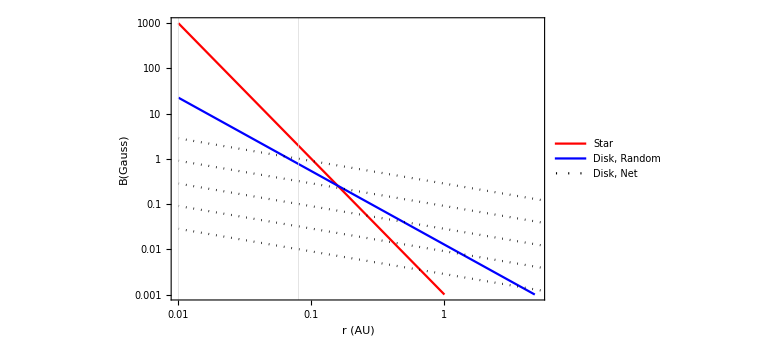

FieldStrengthProfiles.png

```mathematica
plt=LogLogPlot[{Bstar[r],Brand[r],Bnet1[r],Bnet2[r],Bnet3[r],Bnet4[r],Bnet5[r]}, {r,rMin,rMax}, Frame->True,FrameLabel->{"r (AU)", "B(Gauss)"},ImageSize->Large,PlotLegends->Placed[{"Star","Disk, Random", "Disk, Net"},{0.8,0.8}],
BaseStyle->{FontWeight->"Normal",FontSize->14},PlotRange->{{0.01,5},{10^-3,1000}}, GridLines->{{r0star,0.08},{}}, GridLinesStyle->{{Gray},{Gray}},PlotStyle->{{Red},{Blue},{Black, Dotted},{Black, Dotted},{Black, Dotted},{Black, Dotted},{Black, Dotted}}]
Export["FieldStrengthProfiles.png",plt]
```

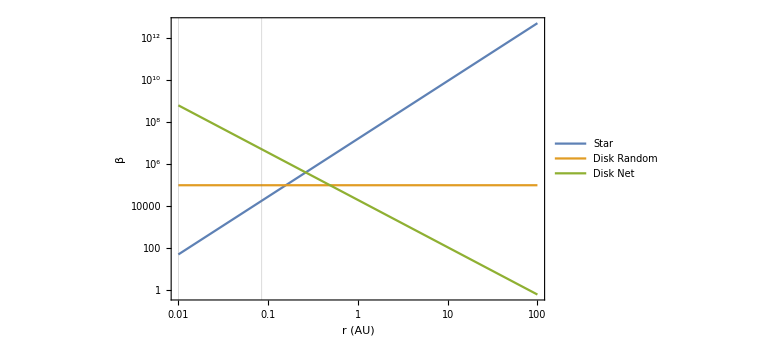

BetaProfiles.png

```mathematica
plt=rloglog[{βstar[r],βrand[r],βnet[r]}, "β",{"Star","Disk Random", "Disk Net"},{{r0star,rMS},{}}]
Export["BetaProfiles.png",plt]
```